(720 (2 n π+n π Cos[n π]-3 Sin[n π]))/(n^4 π^4)

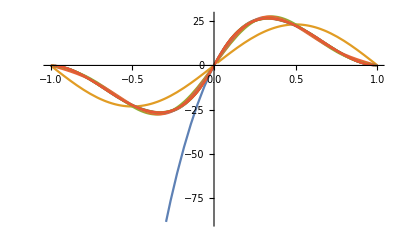

```mathematica
(*Homework #2 Problem 1*)
(*Solve the 1-d heat equation with conditions *)
(*u(0,t)=u(L,t)=0 and u(x,0)=f(x) and 0<x<L*)
(*f(x) = 180x(1-x)^2*)
Clear[a,b,f,L,k,myFSin,myFCos,mTplot,frames]
b[n_]:=Integrate[f[x]*Sin[n*Pi*x/L],{x,0,L}]*(2/L)
f[x_]:=180x*(1-x)^2
L=1;
k=0.3;
b[n]
myFSin[x_,M_]:=Sum[b[n]*Sin[n*Pi*x/L],{n,1,M}]

(*This will Generate a 2-D plot of the series expansion*)
(*of f(x) from the I.C. u(x,0)=f(x) *)
mTplot=Table[Evaluate[myFSin[x,n]],{n,1,10}];
Plot[{f[x],mTplot},{x,-L,L}]
```

```mathematica
(*Now let us consider the general solution*)
G[n_]:=E^(-k*(n*Pi/L)^2*t)
u[x_,t_,M_]:=Sum[b[n]*Sin[n*Pi*x/L]*G[n],{n,1,M}]

frames=Table[Plot3D[Evaluate[u[x,t,10]],{x,0,L},{t,0,k},PlotRange->{0,8}, BoxRatios->{1,1,1}],{k,0.5,5,0.4}];
ListAnimate[frames]
```

```mathematica
(*Problem 1b: 
From the five time snapshots t = 1,2,3,4,5 the solution goes to zero, infact from the 3D plots as t->∞ ⟹ u(x,t)=0. This makes sense because the B.C. conditions suggest that at both end the temperatur is 0, therefore, the initial temperature will be forced temperature f(x)=u(x,0) that is initially given and that will slowly dissipate at t->∞*)
```

(4 n (1+Cos[n π]))/((-9+n^2) π)

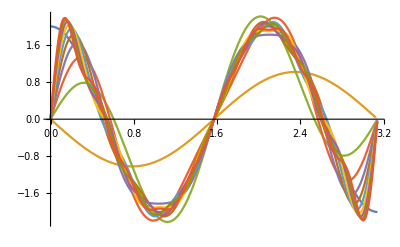

```mathematica
(*Problem 1c let f(x) = 2cos(3x) & L = Pi & k = 1*)
(*Repeat parts b) and c) again*)
Clear[a,b,f,L,k,myFSin,myFCos,mTplot,frames]
b[n_]:=Integrate[f[x]*Sin[n*Pi*x/L],{x,0,L}]*(2/L)
f[x_]:=2*Cos[3*x]
L=Pi;
k=0.1;
b[n]
myFSin[x_,M_]:=Sum[b[2n]*Sin[2n*Pi*x/L],{n,1,M}]

(*This will Generate a 2-D plot of the series expansion*)
(*of f(x) from the I.C. u(x,0)=f(x) *)
mTplot=Table[Evaluate[myFSin[x,n]],{n,1,10}];
Plot[{f[x],mTplot},{x,0,L}]
```

```mathematica
G[n_]:=E^(-k*(n*Pi/L)^2*t)
u[x_,t_,M_]:=Sum[b[2n]*Sin[2n*Pi*x/L]*G[2n],{n,1,M}]

frames=Table[Plot3D[Evaluate[u[x,t,10]],{x,0,L},{t,0,k},PlotRange->{-1,1},ClippingStyle->None,BoxRatios->{1,1,1}],{k,0.1,2.5,.05}];
ListAnimate[frames]
```